## 1) The two-nodes example from DSGC: equation (23)

```mathematica
α=0.1; 
coupling=8; 
power=1; 
γ=0.25;
f1[θ_,ω_,θ1_,ω1_]:=ω;
f2[θ_,ω_,θ1_,ω1_]:=2*power-α*ω-2*coupling*Sin[θ]-γ*ω1;
	(*In case these variables are already defined*)
Clear[θ];
Clear[τ];
eqn={Det[D[{f1[θ,ω,θ1,ω1],f2[θ,ω,θ1,ω1]},{{θ,ω}}]+Exp[-λ*τ]*D[{f1[θ,ω,θ1,ω1],f2[θ,ω,θ1,ω1]},{{θ1,ω1}}]-λ*IdentityMatrix[2]]==0}
```

{0.1 λ+0.25 ⅇ^(-λ τ) λ+1. λ^2+16. Cos[θ]==0}

```mathematica
(*The equation is the same as equation (27) from DSGC*)
```

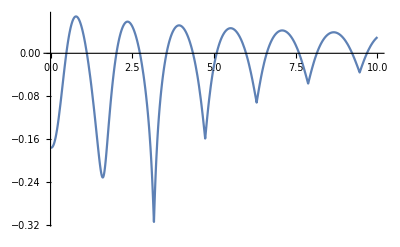

```mathematica
fun[t_?NumericQ]:=Re[λ/.FindRoot[eqn/.{θ->ArcSin[1/8],τ->t}, {λ, RandomComplex[{-1-I,1+I}]}]];
funIter[x_]:=Max[Table[fun[x],50]];
Plot[funIter[x],{x,0,10}]
Clear/@{θ,fun,funIter,f1,f2};
```

```mathematica
(*The graph coincides with that on Figure 6*)
```

## 2) The same model in 4-eq form

```mathematica
numberOfNodes=2;
StarGraph[numberOfNodes]
adjacency=AdjacencyMatrix[StarGraph[numberOfNodes]];
Normal[adjacency](*In normal form*);
power={1,-1};
α=0.1;
γ=0.25;
coupling=8;
```

-Graphics-

### Define the non-delayed Jacobian

```mathematica
(*In case already defined*)
Do[θ[i]=.,{i,1,numberOfNodes}];
funOmega[θ_,ω_,i_List]:=power[[i]]-α*ω[[i]]+Sum[adjacency[[i,j]]*coupling*Sin[θ[[j]]-θ[[i]]],{j,1,numberOfNodes}];
funTheta[θ_,ω_,i_List]:=ω[[i]];
Θ=Array[θ,numberOfNodes]; (*http://reference.wolfram.com/language/tutorial/MakingDefinitionsForIndexedObjects.html*)
Ω=Array[ω,numberOfNodes];
a=D[funTheta[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Θ}];
b=D[funTheta[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Ω}];
c=D[funOmega[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Θ}];
d=D[funOmega[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Ω}];
jac=ArrayFlatten[{{a,b},{c,d}}];
jac//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-8 Cos[θ[1]-θ[2]] | 8 Cos[θ[1]-θ[2]] | -0.1 | 0
8 Cos[θ[1]-θ[2]] | -8 Cos[θ[1]-θ[2]] | 0 | -0.1)

```mathematica
(*Coinside with equation (45) in "Supply networks:Instabilities without overload" up to even number of row and column permutations.
Also similar to equation (25) in DSGC*)
```

### Define the delayed Jacobian

```mathematica
jacD=ArrayFlatten[{{ConstantArray[0,{numberOfNodes,numberOfNodes}],0},{0,-IdentityMatrix[2]*Exp[-λ*τ]*γ}}];
jacD//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -0.25 ⅇ^(-λ τ) | 0.
0 | 0 | 0. | -0.25 ⅇ^(-λ τ))

```mathematica
(*Similar to equation (26) in DSGC*)
```

### Write characteristic equation, construct the function of λ

```mathematica
charEqMatrix=jac+jacD-λ*IdentityMatrix[2*numberOfNodes];
eqn={Det[charEqMatrix]==0};

(*Define 'fixed point'*)
invars=Table[x[i],{i,1,numberOfNodes}];
inconds=Table[{x[i],0},{i,1,numberOfNodes}];
ineqns=Table[power[[i]]==-Sum[adjacency[[i,j]]*coupling*Sin[x[j]-x[i]],{j,1,numberOfNodes}],{i,1,numberOfNodes}];
invals=Table[x[i]/.FindRoot[ineqns,inconds],{i,1,numberOfNodes}];
Do[θ[i]=invals[[i]],{i,1,numberOfNodes}];

eqn
fun[t_?NumericQ]:=Re[λ/.FindRoot[eqn/.{τ->t}, {λ, RandomComplex[{-1-I,1+I}]}]];
funIter[x_]:=Max[Table[fun[x],10]];
```

{1. ⅇ^(-2 λ τ) (0.+3.96863 ⅇ^(λ τ) λ+1.58745 ⅇ^(2 λ τ) λ+0.0625 λ^2+0.05 ⅇ^(λ τ) λ^2+15.8845 ⅇ^(2 λ τ) λ^2+0.5 ⅇ^(λ τ) λ^3+0.2 ⅇ^(2 λ τ) λ^3+1. ⅇ^(2 λ τ) λ^4)==0}

```mathematica
(*Not the same as equation for the case 1). Can than maximal real parts of the eigenvalues be the same?*)
```

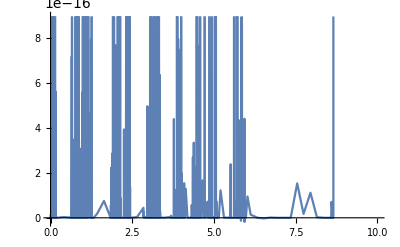

```mathematica
Plot[funIter[x],{x,0,10}]
```

```mathematica
(*The problem may be caused by the root λ=0*)
```

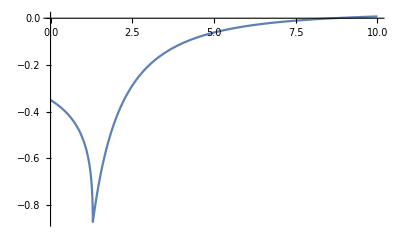

```mathematica
Clear/@{fun,funIter};
eqn={Det[charEqMatrix]/λ==0}; (*divide by λ. No idea why the equation is not reduced then...*)
fun[t_?NumericQ]:=Re[λ/.FindRoot[eqn/.{τ->t}, {λ, RandomComplex[{-1-I,1+I}]}]];
funIter[x_]:=Max[Table[fun[x],10]];
Plot[funIter[x],{x,0,10}]
```

```mathematica
(*The graph is different from the case 1). Why?*)
```

```mathematica
Clear/@{fun,funIter,θ};
power=.;
```

## 3) 4-node star system

### Set the grid parameters, draw the graph

```mathematica
numberOfNodes=4;
StarGraph[numberOfNodes]
adjacency=AdjacencyMatrix[StarGraph[numberOfNodes]];
Normal[adjacency](*In normal form*);
power={3,-1,-1,-1};
α=0.1;
γ=0.25;
coupling=8;
```

-Graphics-

### Define the non-delayed Jacobian

```mathematica
Do[θ[i]=.,{i,1,numberOfNodes}];
funOmega[θ_,ω_,i_List]:=power[[i]]-α*ω[[i]]+Sum[adjacency[[i,j]]*coupling*Sin[θ[[j]]-θ[[i]]],{j,1,numberOfNodes}];
funTheta[θ_,ω_,i_List]:=ω[[i]];
Θ=Array[θ,numberOfNodes]; (*http://reference.wolfram.com/language/tutorial/MakingDefinitionsForIndexedObjects.html*)
Ω=Array[ω,numberOfNodes];
a=D[funTheta[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Θ}];
b=D[funTheta[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Ω}];
c=D[funOmega[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Θ}];
d=D[funOmega[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Ω}];
jac=ArrayFlatten[{{a,b},{c,d}}];
invars=Table[x[i],{i,1,numberOfNodes}];
inconds=Table[{x[i],0},{i,1,numberOfNodes}];
ineqns=Table[power[[i]]==-Sum[adjacency[[i,j]]*coupling*Sin[x[j]-x[i]],{j,1,numberOfNodes}],{i,1,numberOfNodes}];
invals=Table[x[i]/.FindRoot[ineqns,inconds],{i,1,numberOfNodes}]
Do[θ[i]=invals[[i]],{i,1,numberOfNodes}];
jac//MatrixForm
```

{0.125246,-0.0000819561,-0.0000819561,-0.0000819561}

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-23.8118 | 7.93725 | 7.93725 | 7.93725 | -0.1 | 0 | 0 | 0
7.93725 | -7.93725 | 0 | 0 | 0 | -0.1 | 0 | 0
7.93725 | 0 | -7.93725 | 0 | 0 | 0 | -0.1 | 0
7.93725 | 0 | 0 | -7.93725 | 0 | 0 | 0 | -0.1)

### Define the delayed Jacobian

```mathematica
bigt=.;
bigt=2; (*Trying to obtain green curve in Fig 2b) from "Taming instabilities in power grid networks by decentralized control"*)
jacD=ArrayFlatten[{{0,ConstantArray[0,{numberOfNodes,numberOfNodes}]},{IdentityMatrix[numberOfNodes]*(Exp[-λ*(bigt+τ)]-Exp[-λ*τ])*γ/bigt,0}}];
jacD//MatrixForm
λ*IdentityMatrix[2*numberOfNodes]//MatrixForm;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.125 (-ⅇ^(-λ τ)+ⅇ^(-λ (2+τ))) | 0. | 0. | 0. | 0 | 0 | 0 | 0
0. | 0.125 (-ⅇ^(-λ τ)+ⅇ^(-λ (2+τ))) | 0. | 0. | 0 | 0 | 0 | 0
0. | 0. | 0.125 (-ⅇ^(-λ τ)+ⅇ^(-λ (2+τ))) | 0. | 0 | 0 | 0 | 0
0. | 0. | 0. | 0.125 (-ⅇ^(-λ τ)+ⅇ^(-λ (2+τ))) | 0 | 0 | 0 | 0)

### Write characteristic equation, construct the function of λ

```mathematica
charEqMatrix=jac+jacD-λ*IdentityMatrix[2*numberOfNodes];
eqn={Det[charEqMatrix]==0}
fun[t_?NumericQ]:=Re[λ/.FindRoot[eqn/.{τ->t}, {λ, RandomComplex[{-1-I,1+I}]}]];
funIter[x_]:=Max[Table[fun[x],10]];
```

{1. ⅇ^(-4 λ τ-4 λ (2+τ)) (0.000244141 ⅇ^(4 λ τ)+0.000244141 ⅇ^(4 λ (2+τ))-0.000976562 ⅇ^(3 λ τ+λ (2+τ))-0.0930147 ⅇ^(4 λ τ+λ (2+τ))+0.00146484 ⅇ^(2 λ τ+2 λ (2+τ))+0.279044 ⅇ^(3 λ τ+2 λ (2+τ))+8.85937 ⅇ^(4 λ τ+2 λ (2+τ))-0.000976562 ⅇ^(λ τ+3 λ (2+τ))-0.279044 ⅇ^(2 λ τ+3 λ (2+τ))-17.7187 ⅇ^(3 λ τ+3 λ (2+τ))-250.023 ⅇ^(4 λ τ+3 λ (2+τ))+0.0930147 ⅇ^(λ τ+4 λ (2+τ))+8.85937 ⅇ^(2 λ τ+4 λ (2+τ))+250.023 ⅇ^(3 λ τ+4 λ (2+τ))-9.09495×10^-13 ⅇ^(4 λ τ+4 λ (2+τ))-0.00078125 ⅇ^(4 λ τ+λ (2+τ)) λ+0.00234375 ⅇ^(3 λ τ+2 λ (2+τ)) λ+0.223235 ⅇ^(4 λ τ+2 λ (2+τ)) λ-0.00234375 ⅇ^(2 λ τ+3 λ (2+τ)) λ-0.446471 ⅇ^(3 λ τ+3 λ (2+τ)) λ-14.175 ⅇ^(4 λ τ+3 λ (2+τ)) λ+0.00078125 ⅇ^(λ τ+4 λ (2+τ)) λ+0.223235 ⅇ^(2 λ τ+4 λ (2+τ)) λ+14.175 ⅇ^(3 λ τ+4 λ (2+τ)) λ+200.019 ⅇ^(4 λ τ+4 λ (2+τ)) λ-0.0078125 ⅇ^(4 λ τ+λ (2+τ)) λ^2+0.0234375 ⅇ^(3 λ τ+2 λ (2+τ)) λ^2+2.23329 ⅇ^(4 λ τ+2 λ (2+τ)) λ^2-0.0234375 ⅇ^(2 λ τ+3 λ (2+τ)) λ^2-4.46658 ⅇ^(3 λ τ+3 λ (2+τ)) λ^2-141.929 ⅇ^(4 λ τ+3 λ (2+τ)) λ^2+0.0078125 ⅇ^(λ τ+4 λ (2+τ)) λ^2+2.23329 ⅇ^(2 λ τ+4 λ (2+τ)) λ^2+141.929 ⅇ^(3 λ τ+4 λ (2+τ)) λ^2+2005.86 ⅇ^(4 λ τ+4 λ (2+τ)) λ^2+0.01875 ⅇ^(4 λ τ+2 λ (2+τ)) λ^3-0.0375 ⅇ^(3 λ τ+3 λ (2+τ)) λ^3-3.57226 ⅇ^(4 λ τ+3 λ (2+τ)) λ^3+0.01875 ⅇ^(2 λ τ+4 λ (2+τ)) λ^3+3.57226 ⅇ^(3 λ τ+4 λ (2+τ)) λ^3+113.448 ⅇ^(4 λ τ+4 λ (2+τ)) λ^3+0.09375 ⅇ^(4 λ τ+2 λ (2+τ)) λ^4-0.1875 ⅇ^(3 λ τ+3 λ (2+τ)) λ^4-17.8738 ⅇ^(4 λ τ+3 λ (2+τ)) λ^4+0.09375 ⅇ^(2 λ τ+4 λ (2+τ)) λ^4+17.8738 ⅇ^(3 λ τ+4 λ (2+τ)) λ^4+568.429 ⅇ^(4 λ τ+4 λ (2+τ)) λ^4-0.15 ⅇ^(4 λ τ+3 λ (2+τ)) λ^5+0.15 ⅇ^(3 λ τ+4 λ (2+τ)) λ^5+14.2911 ⅇ^(4 λ τ+4 λ (2+τ)) λ^5-0.5 ⅇ^(4 λ τ+3 λ (2+τ)) λ^6+0.5 ⅇ^(3 λ τ+4 λ (2+τ)) λ^6+47.6835 ⅇ^(4 λ τ+4 λ (2+τ)) λ^6+0.4 ⅇ^(4 λ τ+4 λ (2+τ)) λ^7+1. ⅇ^(4 λ τ+4 λ (2+τ)) λ^8)==0}

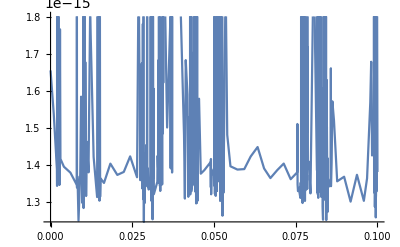

```mathematica
Plot[funIter[x],{x,0,0.1}]
```

```mathematica
(*λ=0 is not an obvious root from the equation, but seems to be that from the Graph*)
```